H(ⅉω)= 40/((1+(ⅈ ω)/4) (1+(ⅈ ω)/3) (1+(ⅈ ω)/2) (1+ⅈ ω))

|H(ω)| = (20 Log[40])/Log[10]-(20 Log[Abs[1+(ⅈ ω)/4]])/Log[10]-(20 Log[Abs[1+(ⅈ ω)/3]])/Log[10]-(20 Log[Abs[1+(ⅈ ω)/2]])/Log[10]-(20 Log[Abs[1+ⅈ ω]])/Log[10]

Plot::invpr: Value of option PlotRange is not compatible with the option ScalingFunctions -> {{Log,Exp},{Log,Exp}}

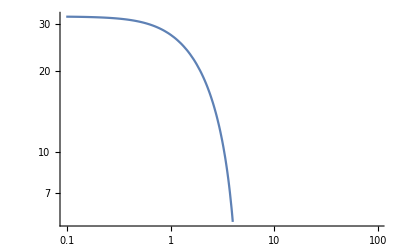

```mathematica
(*Start of Program*)
Clear["Global`*"]
K=Input["Enter The Value Of Gain"];
n = Input["Enter The Number Of Poles"];
listOfPoles =Table[Input["Enter The Value Of A Pole"],n];
listOfTerms=20*Log[10,Abs[(1+(ⅉ ω)/#)&[listOfPoles]]];
largestPole=Max[listOfPoles];
(*H=Times@@listOfTerms*)
H[ω_]:=K*Times@@(1/(1+(ⅉ*ω)/#))&[listOfPoles](*This makes the function ∏_(i=1)^n 1/(1+ⅉω/Subscript[p, i])*)
StringForm["H(ⅉω)= ``",H[ω]]
peakMag = FindMaximum[Abs[H[ω]],ω][[1]];
peakdB= 20*Log[10,K];
dB[ω_]:=peakdB+(Plus@@-listOfTerms)
StringForm["|H(ω)| = ``", dB[ω]]
LogLogPlot[dB[ω],{ω,0,100},PlotRange->{{0,100},{0,peakdB}}]
```